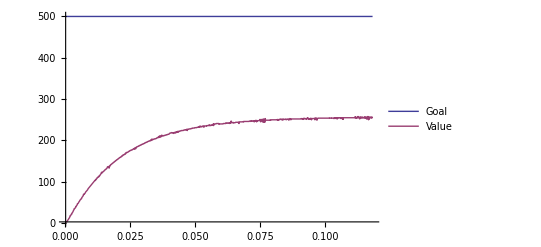

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data.txt","Table"];
data=data[[2;;]];
goaldata=Transpose[Transpose[data][[1;;2]]];
adcdata=Transpose[{Transpose[data][[1]],Transpose[data][[3]]}];
voltage=Transpose[{Transpose[data][[1]],2*Transpose[data][[4]]}];
ListLinePlot[{goaldata[[;;]],adcdata[[;;]](*,voltage*)},PlotRange->All,PlotLegends->{"Goal","Value"}]
```

```mathematica
a=goaldata[[1]][[2]]
```

500

```mathematica
b=N[Mean[ Transpose[adcdata[[-100;;-1]]][[2]]]]
```

255.29

```mathematica
t0=goaldata[[1]][[1]]
```

0.000063021

```mathematica
t2=Select[adcdata,#[[2]]>b/2&][[1]][[1]]
```

0.015099

```mathematica
t3=Select[adcdata,#[[2]]>0.632*b&][[1]][[1]]
```

0.021791

```mathematica
t1=(t2-t3*Log[2])/(1-Log[2])
```

-0.0000175009

```mathematica
τ=t3-t1
```

0.0218085

```mathematica
τdel=t1-t0
```

-0.0000805219

```mathematica
k=b/a
```

0.51058

```mathematica
r=τdel/τ
```

-0.00369223

```mathematica
p=1/r/k*(1+r/3)
pi={1/r/k*(.9+r/12),τ*((30+3r)/(9+20r))}
pid={1/r/k*(4/3+r/4),τdel((32+6r)/(13+8r)),4τ/(11+2r)}
```

-529.801

{-477.245,0.0732693}

{-706.782,-0.000198522,0.00793569}